```mathematica
ComplexPlot3D[(z^2+1)/(z^2-1),{z,-2-2I,2+2I}]
```

-Graphics3D-

```mathematica
Sin[Pi/2]
```

1

```mathematica
f[x_,y_,t_]:=Sin[x+y^2 -t]
```

```mathematica
f[2,2]
```

Sin[6]

```mathematica
N[%,3]
```

-0.279

```mathematica
Animate[
	Plot3D[f[x,y,t],{x,-3,3},{y,-2,2}],
	{t,0,10}
]
```

CH1: 曲线拟合

```mathematica
k:=2x
```

```mathematica
k /.x->4
```

8

```mathematica
g[x_]:=7x^2+4x+1
g[x]/.x->1
```

```mathematica
Table[{x,g[x]},{x,-2,2,0.1}]
```

{{-2.,21.},{-1.9,18.67},{-1.8,16.48},{-1.7,14.43},{-1.6,12.52},{-1.5,10.75},{-1.4,9.12},{-1.3,7.63},{-1.2,6.28},{-1.1,5.07},{-1.,4.},{-0.9,3.07},{-0.8,2.28},{-0.7,1.63},{-0.6,1.12},{-0.5,0.75},{-0.4,0.52},{-0.3,0.43},{-0.2,0.48},{-0.1,0.67},{0.,1.},{0.1,1.47},{0.2,2.08},{0.3,2.83},{0.4,3.72},{0.5,4.75},{0.6,5.92},{0.7,7.23},{0.8,8.68},{0.9,10.27},{1.,12.},{1.1,13.87},{1.2,15.88},{1.3,18.03},{1.4,20.32},{1.5,22.75},{1.6,25.32},{1.7,28.03},{1.8,30.88},{1.9,33.87},{2.,37.}}

```mathematica
tb=%
```

{{-2.,21.},{-1.9,18.67},{-1.8,16.48},{-1.7,14.43},{-1.6,12.52},{-1.5,10.75},{-1.4,9.12},{-1.3,7.63},{-1.2,6.28},{-1.1,5.07},{-1.,4.},{-0.9,3.07},{-0.8,2.28},{-0.7,1.63},{-0.6,1.12},{-0.5,0.75},{-0.4,0.52},{-0.3,0.43},{-0.2,0.48},{-0.1,0.67},{0.,1.},{0.1,1.47},{0.2,2.08},{0.3,2.83},{0.4,3.72},{0.5,4.75},{0.6,5.92},{0.7,7.23},{0.8,8.68},{0.9,10.27},{1.,12.},{1.1,13.87},{1.2,15.88},{1.3,18.03},{1.4,20.32},{1.5,22.75},{1.6,25.32},{1.7,28.03},{1.8,30.88},{1.9,33.87},{2.,37.}}

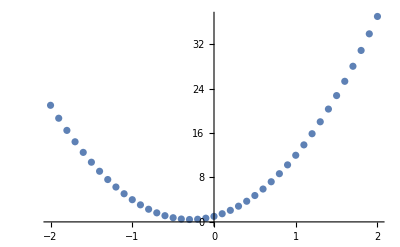

```mathematica
ListPlot[tb]
```

```mathematica
Fit[tb,{1,x,x^2},x]
```

1.+4. x+7. x^2

```mathematica
fn=%
```

1.+4. x+7. x^2

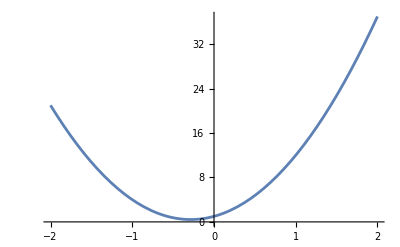

```mathematica
Plot[fn,{x,-2,2}]
```

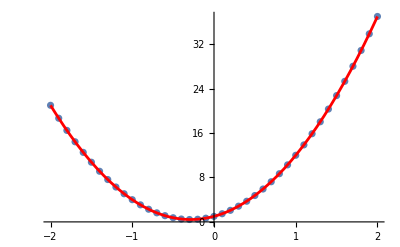

```mathematica
Show[{
	ListPlot[tb],
	Plot[fn,{x,-2,2},PlotStyle->Red]
}]
```

CH2:求导，求积分

```mathematica
1/3
```

1/3

```mathematica
N[%,3]
```

0.333333

```mathematica
1/3//N
```

0.333333

```mathematica
Cos'[x]
```

-Sin[x]

```mathematica
Cos''[x]
```

-Cos[x]

```mathematica
D[x^3,{x,3}]#三阶导数
```

```mathematica
6 #三阶导数
Integrate[x,x]
```

6 #三阶导数

x^2/2

```mathematica
Integrate[Log[x], {x, 1, 2}]#传统表达式ctrlshift和t #输出ctrlshift加i
```

```mathematica
-1+Log[4]
```

-1+Log[4]

```mathematica
N[%,4]
```

0.3863

CH3： 隐函数求导
		试求x^2+4y^2=4在x=1处的斜率

```mathematica
Solve[3x==6,x]
```

{{x→2}}

```mathematica
suf[x_,y_]:=x^2+4y^2
```

```mathematica
Plot3D[suf[x,y],{x,-4,4},{y,-3,3}]
```

-Graphics3D-

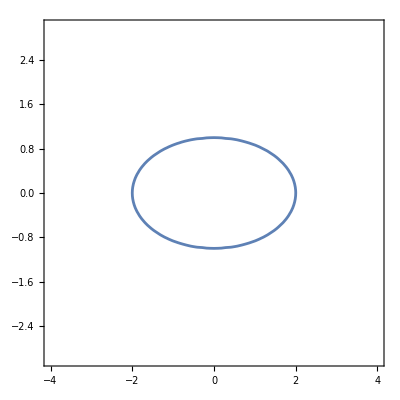

```mathematica
ContourPlot[suf[x,y]==4,{x,-4,4},{y,-3,3}]
```

```mathematica
Clear[y]
```

```mathematica
D[x^2+4y[x]^2==4,x]
```

```mathematica
2 x+8 y[x] y'[x]==0
Solve[%,y'[x]]
```

2 x+8 y[x] y'[x]==0

{{y'[x]→-x/(4 y[x])}}

```mathematica
x^2+4 y^2==4/.x->1
```

```mathematica
1+4 y^2==4
```

1+4 y^2==4

```mathematica
Solve[%,y]
```

{{y→-(√3)/2},{y→(√3)/2}}

```mathematica
tan = -1/(4y)
```

```mathematica
-1/(4 y)
tan/.%%
```

-1/(4 y)

{1/(2 √3),-1/(2 √3)}

{{x→2}}

CH4: 解微分方程 , mf(x)’’+kf(x)=0

```mathematica
Clear[m,k]
```

```mathematica
DSolve[m f''[x] + k f[x] == 0, f[x], x]
```

```mathematica
{{f[x]->C[1] Cos[(√k x)/(√m)]+C[2] Sin[(√k x)/(√m)]}} #记得清除先前符号的数值亦或者用module类似于jupyter的block
```

```mathematica
Simplify[{{f[x]->AiryAi[-(2^(1/3) x)/((-1/m)^(2/3) m)] C[1]+AiryBi[-(2^(1/3) x)/((-1/m)^(2/3) m)] C[2]}}]
```